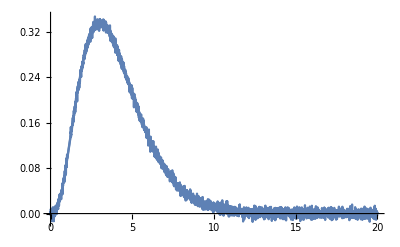

```mathematica
f[x_,a_,b_,c_]:= a x^b Exp[-c x];
fN[x_,a_,b_,c_]:= a x^b Exp[-c x]+RandomVariate[NormalDistribution[0,0.005]];
Show[{
Plot[f[x,0.25,3,1],{x, 0,20}, PlotRange->All],
Plot[fN[x,0.25,3,1],{x, 0,20}, PlotRange->All]
}
]
```

```mathematica
RandomVariate[NormalDistribution[0.005,0.0001]]
```

0.00499253

```mathematica
RandomVariate[NormalDistribution[0,0.5]]
```

0.0477901

```mathematica
data= Table[{N[(i*1.0)/5],fN[N[(i*1.0)/5],0.25,3,1],RandomVariate[NormalDistribution[0.005,0.0001]] },{i,100}];
Export["/home/jsanchez/Documents/Fitting/data.dat",data]
```

/home/jsanchez/Documents/Fitting/data.dat

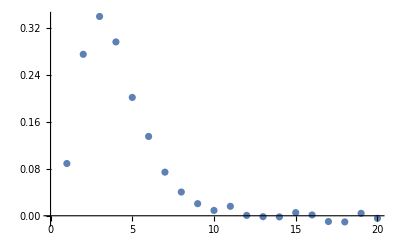

```mathematica
data= Table[{N[i*1.0],fN[N[i*1.0],0.25,3,1] },{i,20}];
ListPlot[data]
```

a ⅇ^(-c t) t^d

{a→0.254822,c→1.03023,d→3.0752}

Function[{t},0.254822 ⅇ^(-1.03023 t) t^3.0752]

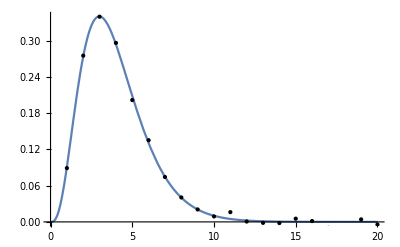

```mathematica
model = a t^d Exp[-c t]
fit = FindFit[data,model,{a,c,d},t]
modelf=Function[{t},Evaluate[model/. fit]]
Plot[modelf[t],{t,0,20},Epilog->Map[Point,data]]
```

{a→14.3889,k→0.198208}

Function[{t},14.3889 ⅇ^(-0.198208 t)]

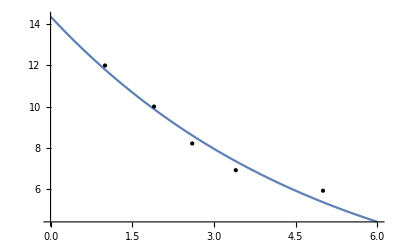

```mathematica
data={{1.0,12.},{1.9,10.},{2.6,8.2},{3.4,6.9},{5.0,5.9}};
model=a Exp[-k t];
fit=FindFit[data,model,{a,k},t]
modelf=Function[{t},Evaluate[model/. fit]]
Plot[modelf[t],{t,0,6},Epilog->Map[Point,data]]
```